```mathematica
Clear["Global`*"];
```

```mathematica
h=0.100; w=0.050;αp=π/6;d=0.050; ρ=7800;M=h w d ρ
```

1.95

```mathematica
b=Cos[αp]/2 (w Tan[αp]+h)
```

0.0558013

```mathematica
a=√((h^2+w^2)/4) Cos[π/2+αp-ArcTan[w/h]]
```

-0.00334936

```mathematica
c=√((h^2+w^2)/4);
```

```mathematica
θs=(w h)/3(w^2+h^2);
```

```mathematica
θo=θs+M c^2
```

0.00611458

```mathematica
DrawRectangle[{x_,y_,r_}]:={EdgeForm[Black],
Translate[
Rotate[
{
Pink,Rectangle[{0,0},{w,h}]
},
r,{0,0}
],
{x,y}
],Gray,Rectangle[{-h-w,0},{h+w,-w/10}]
}
rect[angle_]:=Graphics[DrawRectangle[{0,0,angle}]
,PlotRange->{{-w-h,h+ w},{-w,h+w}},ImageSize->300]
```

```mathematica
Manipulate[rect[α],{α,0,π/2}]
```

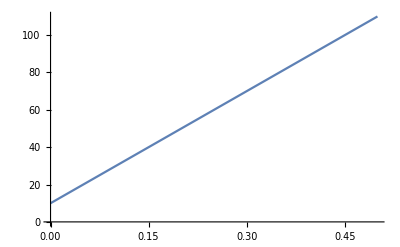

```mathematica
F=120(UnitStep[t]-UnitStep[t-0.01]-UnitStep[t-0.15]+UnitStep[t-0.16]); 
F=120 Sin[100t];
F=200 t+10;
Plot[F,{t,0,0.5}]
```

```mathematica
b=Cos[α[t]]/2 (w Tan[α[t]]+h);
a=√((h^2+w^2)/4) Cos[π/2+α[t]-ArcTan[w/h]];
g=9.81;K=M g;
eq1=x''[t] M==-F;
eq2=y''[t] M==K-M g;
eq3=α''[t] θo==F b-(K+M g)a;
Sol3=First@NDSolve[{eq3,α[0]==0,α'[0]==0},α[t],{t,0,1}];
αBounded=Piecewise[
{
{0,Evaluate[α[t]/.Sol3]<0},
{π/2,Evaluate[α[t]/.Sol3]>π/2},
{Evaluate[α[t]/.Sol3],Evaluate[α[t]/.Sol3]>0}}];
Plot[αBounded,{t,0,.5},PlotRange->All];
```

```mathematica
Manipulate[
Module[{α1,F1},
α1=αBounded/.t->t1;
F1=-0.0005 F/.t->t1;
plots=Row[{Plot[αBounded,{t,0,.5},PlotRange->All,ImageSize->300,PlotTheme->"Scientific",PlotLabel->"α[-]",Epilog->{Red,PointSize[Large],Point[{t1,α1}]},PlotStyle->Dashed],
Show[rect[α1],Graphics[{Blue,Arrow[{{c Cos[α1+π/2-ArcTan[w/h]],c Sin[α1+π/2-ArcTan[w/h]]},{F1+c Cos[α1+π/2-ArcTan[w/h]],c Sin[α1+π/2-ArcTan[w/h]]}}],Text[Style["F",Blue,Large],({F1+c Cos[α1+π/2-ArcTan[w/h]],c Sin[α1+π/2-ArcTan[w/h]]}) 1.2]}]]}]
],
{t1,0,0.5,Appearance->"Labeled"}]
```

```mathematica
Module[{F1,α1},
α1=αBounded/.t->t1;
F1=-0.0005 F/.t->t1;
Anim=Table[Row[{Plot[αBounded,{t,0,.5},PlotRange->All,ImageSize->300,PlotTheme->"Scientific",PlotLabel->"α[-]",Epilog->{Red,PointSize[Large],Point[{t1,α1}]},PlotStyle->Dashed],
Show[rect[α1],Graphics[{Blue,Arrow[{{c Cos[α1+π/2-ArcTan[w/h]],c Sin[α1+π/2-ArcTan[w/h]]},{F1+c Cos[α1+π/2-ArcTan[w/h]],c Sin[α1+π/2-ArcTan[w/h]]}}],Text[Style["F",Blue,Large],({F1+c Cos[α1+π/2-ArcTan[w/h]],c Sin[α1+π/2-ArcTan[w/h]]}) 1.2]}]]}],{t1,0.0000001,0.5,.005}];
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
(*Export["anim.gif",Anim]*)
```

C:\Users\EDU_UGEX_7219\Google Drive\MSc\Thesis

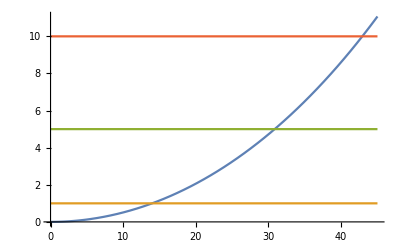

```mathematica
Plot[{Abs[x π/180-Sin[x π/180]]/Abs[Sin[x π/180]]*100,1,5,10},{x,0,45}]
```